```mathematica
Phi1[x_].=1-5.96168047527760*10^-47 Cosh[52.06761235859028x]-6.78355315350872*10^-56 Cosh[62.76152118553390 x] - 7.20274049646598*10^-84 Cosh[95.14161078659372 x]-6.34541150517664*10^-238Cosh[272.5766481169758x]
```

```mathematica
Phi1[2]
```

0.500986

```mathematica
Phi2[x_]:= 1.685808767651539*10^3Exp[-5.206761235859028x] +3.143867366942945*10^4Exp[-6.276152118553390x]+2.879977113018352*10^7Exp[-9.514161078659372x]+ 8.594190506002560*10^22Exp[-27.25766481169758x]+1.298426035202193*10^-36Exp[27.25766481169758x ]+ 1.432344656303454*10^-13Exp[9.514161078659372x]+
1.514562265056083*10^-9Exp[6.276152118553390x]+ 1.594431209450755*10^-8Exp[5.206761235859028x]
```

```mathematica
Phi2[2]
```

0.500986

```mathematica
Phi4[x_] :=10-0.1983746883968300Exp[0.5254295183311557x]- 7.824765332896027*10^-5Exp[1.108937229227813x]-9.746660212187006*10^-6 Exp[1.615640334315550x]-2.895098351422132*10^-13 Exp[4.554850586269065x]-75.34793864805979 Exp[-0.5254295183311557x]-20.42874998426011 Exp[-1.108937229227813x]-7.129175418204712*10^2 Exp[-1.615640334315550x]-2.716409367577795*10^9*Exp[-4.554850586269065x]
```

```mathematica
Phi5[x_]:=31.53212162577067 Exp[-0.5254295183311557x]+26.25911060454856 Exp[-1.108937229227813x] + 1.841223066417334*10^3 Exp[-1.615640334315550x]+1.555593549394869 *10^11 Exp[-4.554850586269065x]-3.119310353653182*10^-3 Exp[0.5254295183311557x]-6.336401143340483*10^-7*Exp[1.108937229227813x] - 3.528757679361232*10^-8*Exp[1.615640334315550x] - 4.405514335746888*10^-18*Exp[4.554850586269065x]
```

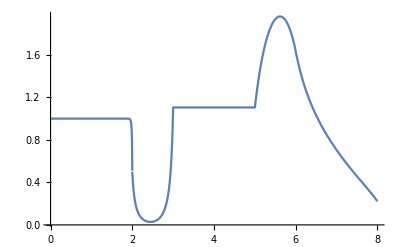

```mathematica
Plot[If[x<2,Phi1[x],If[x<3,Phi2[x],If[x<5,1.105109108062394,If[x<6,Phi4[x],Phi5[x]]]]],{x,0,8},PlotRange->All,PlotPoints->1000]
```

```mathematica
TotalFunc[x_]:=If[x<2,Phi1[x],If[x<3,Phi2[x],If[x<5,1.105109108062394,If[x<6,Phi4[x],Phi5[x]]]]]
```

```mathematica
ReedTable=Table[{N[x],N[TotalFunc[x],8]},{x,0,8,1/10}]
```

{{0.,1.},{0.1,1.},{0.2,1.},{0.3,1.},{0.4,1.},{0.5,1.},{0.6,1.},{0.7,1.},{0.8,1.},{0.9,1.},{1.,1.},{1.1,1.},{1.2,1.},{1.3,1.},{1.4,1.},{1.5,1.},{1.6,1.},{1.7,1.},{1.8,0.999998},{1.9,0.999506},{2.,0.500986},{2.1,0.163648},{2.2,0.0769114},{2.3,0.0424216},{2.4,0.0295472},{2.5,0.0300272},{2.6,0.0438279},{2.7,0.0785153},{2.8,0.155674},{2.9,0.345406},{3.,1.10511},{3.1,1.10511},{3.2,1.10511},{3.3,1.10511},{3.4,1.10511},{3.5,1.10511},{3.6,1.10511},{3.7,1.10511},{3.8,1.10511},{3.9,1.10511},{4.,1.10511},{4.1,1.10511},{4.2,1.10511},{4.3,1.10511},{4.4,1.10511},{4.5,1.10511},{4.6,1.10511},{4.7,1.10511},{4.8,1.10511},{4.9,1.10511},{5.,1.10511},{5.1,1.39588},{5.2,1.60983},{5.3,1.76457},{5.4,1.87099},{5.5,1.93538},{5.6,1.96074},{5.7,1.94729},{5.8,1.89252},{5.9,1.79065},{6.,1.63147},{6.1,1.46092},{6.2,1.32473},{6.3,1.21198},{6.4,1.11558},{6.5,1.03092},{6.6,0.954922},{6.7,0.885531},{6.8,0.82133},{6.9,0.76132},{7.,0.704768},{7.1,0.651111},{7.2,0.599892},{7.3,0.550712},{7.4,0.503189},{7.5,0.456926},{7.6,0.411463},{7.7,0.366224},{7.8,0.320431},{7.9,0.272976},{8.,0.222226}}

```mathematica
Save["ReedSol.csv",ReedTable]
```

```mathematica
Directory[]
```

/Users/ryanmcclarren